```mathematica
(**Common Definitions**)
```

```mathematica
Q=1.82;Subscript[x, B]=0.34;M=0.938272;k=5.75;t=0.17;
```

```mathematica
(*Define β*)
```

```mathematica
β=(2 Subscript[x, B] M)/Sqrt[Q]
```

0.472936

```mathematica
(*Define y*)
```

```mathematica
y=Sqrt[Q]/(k β)
```

0.496096

```mathematica
(*Twist 3 Subscript[h, 3]^U=OverTilde[Subscript[h, 3]^U]*)
```

```mathematica
Subscript[h, 3U]:=(2 Subscript[x, B](y-2)Sqrt[(t(Subscript[x, B]-1)-M^2 Subscript[x, B]^2)(1-y)](β-1)Cos[ϕ*π/180])/((1+(β-1)Subscript[x, B])y^2)
```

```mathematica
(*Common Definitions*)
```

```mathematica
Subscript[Q, 1]=4.55;Subscript[x, B1]=0.37;M=0.938272;k=5.75;Subscript[t, 1]=0.26;
```

```mathematica
(*Define Subscript[β, 1]*)
```

```mathematica
Subscript[β, 1]=(2 Subscript[x, B1] M)/Sqrt[Subscript[Q, 1]]
```

0.325503

```mathematica
(*Define Subscript[y, 1]*)
```

```mathematica
Subscript[y, 1]=Sqrt[Subscript[Q, 1]]/(k Subscript[β, 1])
```

1.13968

```mathematica
(*Twist 3 Subscript[h, 3]^U1=OverTilde[Subscript[h, 3]^U1]*)
```

```mathematica
Subscript[h, 3U1]=(2 Subscript[x, B1](Subscript[y, 1]-2)Sqrt[(Subscript[t, 1](Subscript[x, B1]-1)-M^2 Subscript[x, B1]^2)(1-Subscript[y, 1])](Subscript[β, 1]-1)Cos[ϕ*π/180])/((1+(Subscript[β, 1]-1)Subscript[x, B1])Subscript[y, 1]^2)
```

0.0877938 Cos[(π ϕ)/180]

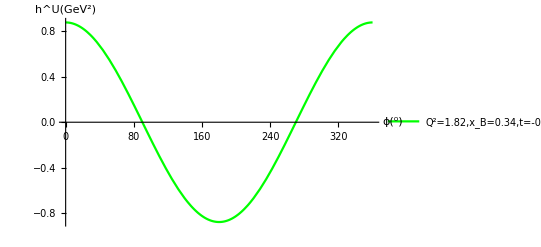

```mathematica
P1=Plot[Im[Subscript[h, 3U]],{ϕ,0,360},PlotStyle->Green,PlotLegends->{"Q^2=1.82,x_B=0.34,t=-0.17"},AxesLabel->{"ϕ(^0)","h^U(GeV^2)"}]
```

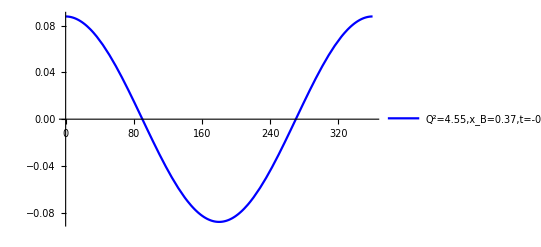

```mathematica
P2=Plot[Subscript[h, 3U1],{ϕ,0,360},PlotRange->All,PlotStyle->Blue,PlotLegends->{"Q^2=4.55,x_B=0.37,t=-0.26"}]
```

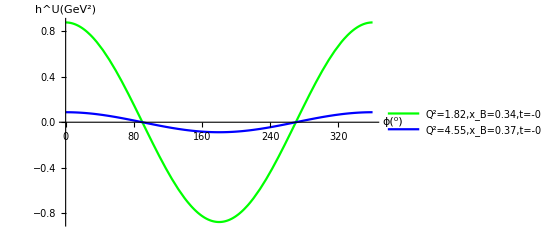

```mathematica
Show[P1,P2]
```